```mathematica
DSolve[y'[x]==(3-2 x)y[x],y[x],x]
```

{{y[x]→ⅇ^(3 x-x^2) C[1]}}

```mathematica
ff[x_]=C ⅇ^(3 x-x^2);
```

```mathematica
listFF=Table[ff[x],{C,-5,5}];
```

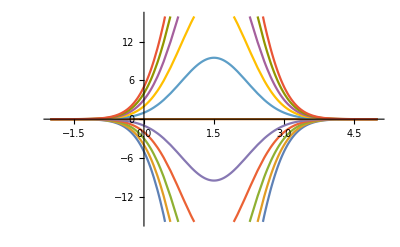

```mathematica
Plot[listFF,{x,-2,5}]
```

```mathematica
Series[Sin[x],{x,0,9}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10

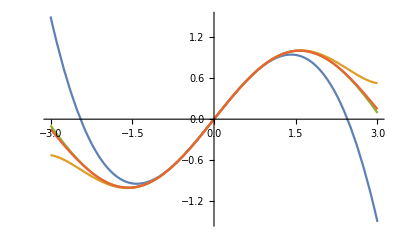

```mathematica
Plot[{x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880},{x,-3,3}]
```